```mathematica
ex = {1,0,0};
ey = {0,1,0};
ez= {0,0,1};
Ndemag= {{0, 0,0},{0,0,0},{0 , 0,1}};
```

```mathematica
m[θ_,ϕ_] :={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
M[Ms_,θ_,ϕ_] :=Ms*m[θ,ϕ];
Ezeeman[Ms_,θ_,ϕ_,H_] :=-μ H Ms *m[θ,ϕ].ey;
Edem[Ms_,θ_,ϕ_]:=μ/2*Ms^2*m[θ,ϕ].(Ndemag.m[θ,ϕ]);
Eani[Ms_,Keff_,θ_,ϕ_]:=-Keff (ez.m[θ,ϕ])^2;
(*Eani2[Ms_,Keff2_,θ_,ϕ_]:=-Keff2 (ez.m[θ,ϕ])^4;*)
(*Estr[Ms_,θ_,ϕ_, Hstr_] := -μ Hstr Ms*m[θ,ϕ].{0,0,1};*)
(*Etot[Ms_,K_,K2_,θ_,ϕ_,H_,Hstr_] := Ezeeman[Ms,θ,ϕ,H ]+Eani[Ms,K,θ,ϕ]+Eani2[Ms,K2,θ,ϕ]+Edem[Ms,θ,ϕ]+Estr[Ms,θ,ϕ,Hstr];*)
Etot[Ms_,K_,θ_,ϕ_,H_] := Ezeeman[Ms,θ,ϕ,H ]+Eani[Ms,K,θ,ϕ]+Edem[Ms,θ,ϕ];

(*Reduce[-H Cos[θ]+Hstr Sin[θ/2]+Heff Cos[θ] Sin[θ]==0,θ]/.{C[1]->  0};*)
```

```mathematica
Series[Etot[Ms,Keff,Pi/2,ϕ,H],{θ,θ0,1}]
```

(-Keff Cos[θ0]^2+1/2 Ms^2 μ Cos[θ0]^2-H Ms μ Sin[θ0] Sin[ϕ])+(2 Keff Cos[θ0] Sin[θ0]-Ms^2 μ Cos[θ0] Sin[θ0]-H Ms μ Cos[θ0] Sin[ϕ]) (θ-θ0)+O[θ-θ0]^2

```mathematica
t= θ/.Solve[-H Cos[θ]+Hstr Sin[θ-a*H]+Keff Cos[θ] Sin[θ]==0,θ]/.{C[1]->0};
```

```mathematica
t//Length
```

8

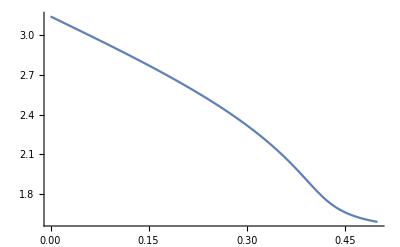

```mathematica
Plot[t[[2]]/.{Hstr -> -0.03, Keff  ->  0.35,a -> 3},{H,0,0.5}]
```

```mathematica
θ[H_,Keff_,Hstr_,a_]:= ArcCos[-(Hstr Cos[a H])/(2 Keff)-1/2 √((Hstr^2 Cos[a H]^2)/Keff^2-(2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2))/(3 Keff^2)+(2^(1/3) (H^2+Hstr^2-Keff^2+2 H Hstr Sin[a H])^2)/(3 Keff^2 (108 Hstr^2 Keff^4 Cos[a H]^2-108 Hstr^4 Keff^2 Cos[a H]^4+108 Hstr^2 Keff^2 Cos[a H]^2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)+2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^3+√(-4 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^6+(108 Hstr^2 Keff^4 Cos[a H]^2-108 Hstr^4 Keff^2 Cos[a H]^4+108 Hstr^2 Keff^2 Cos[a H]^2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)+2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^3)^2))^(1/3))+1/(3 2^(1/3) Keff^2)(108 Hstr^2 Keff^4 Cos[a H]^2-108 Hstr^4 Keff^2 Cos[a H]^4+108 Hstr^2 Keff^2 Cos[a H]^2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)+2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^3+√(-4 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^6+(108 Hstr^2 Keff^4 Cos[a H]^2-108 Hstr^4 Keff^2 Cos[a H]^4+108 Hstr^2 Keff^2 Cos[a H]^2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)+2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^3)^2))^(1/3))-1/2 √((2 Hstr^2 Cos[a H]^2)/Keff^2-(4 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2))/(3 Keff^2)-(2^(1/3) (H^2+Hstr^2-Keff^2+2 H Hstr Sin[a H])^2)/(3 Keff^2 (108 Hstr^2 Keff^4 Cos[a H]^2-108 Hstr^4 Keff^2 Cos[a H]^4+108 Hstr^2 Keff^2 Cos[a H]^2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)+2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^3+√(-4 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^6+(108 Hstr^2 Keff^4 Cos[a H]^2-108 Hstr^4 Keff^2 Cos[a H]^4+108 Hstr^2 Keff^2 Cos[a H]^2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)+2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^3)^2))^(1/3))-1/(3 2^(1/3) Keff^2)(108 Hstr^2 Keff^4 Cos[a H]^2-108 Hstr^4 Keff^2 Cos[a H]^4+108 Hstr^2 Keff^2 Cos[a H]^2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)+2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^3+√(-4 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^6+(108 Hstr^2 Keff^4 Cos[a H]^2-108 Hstr^4 Keff^2 Cos[a H]^4+108 Hstr^2 Keff^2 Cos[a H]^2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)+2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^3)^2))^(1/3)-((16 Hstr Cos[a H])/Keff-(8 Hstr^3 Cos[a H]^3)/Keff^3+(8 Hstr Cos[a H] (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2))/Keff^3)/(4 √((Hstr^2 Cos[a H]^2)/Keff^2-(2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2))/(3 Keff^2)+(2^(1/3) (H^2+Hstr^2-Keff^2+2 H Hstr Sin[a H])^2)/(3 Keff^2 (108 Hstr^2 Keff^4 Cos[a H]^2-108 Hstr^4 Keff^2 Cos[a H]^4+108 Hstr^2 Keff^2 Cos[a H]^2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)+2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^3+√(-4 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^6+(108 Hstr^2 Keff^4 Cos[a H]^2-108 Hstr^4 Keff^2 Cos[a H]^4+108 Hstr^2 Keff^2 Cos[a H]^2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)+2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^3)^2))^(1/3))+1/(3 2^(1/3) Keff^2)(108 Hstr^2 Keff^4 Cos[a H]^2-108 Hstr^4 Keff^2 Cos[a H]^4+108 Hstr^2 Keff^2 Cos[a H]^2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)+2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^3+√(-4 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^6+(108 Hstr^2 Keff^4 Cos[a H]^2-108 Hstr^4 Keff^2 Cos[a H]^4+108 Hstr^2 Keff^2 Cos[a H]^2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)+2 (H^2-Keff^2+Hstr^2 Cos[a H]^2+2 H Hstr Sin[a H]+Hstr^2 Sin[a H]^2)^3)^2))^(1/3))))]
```

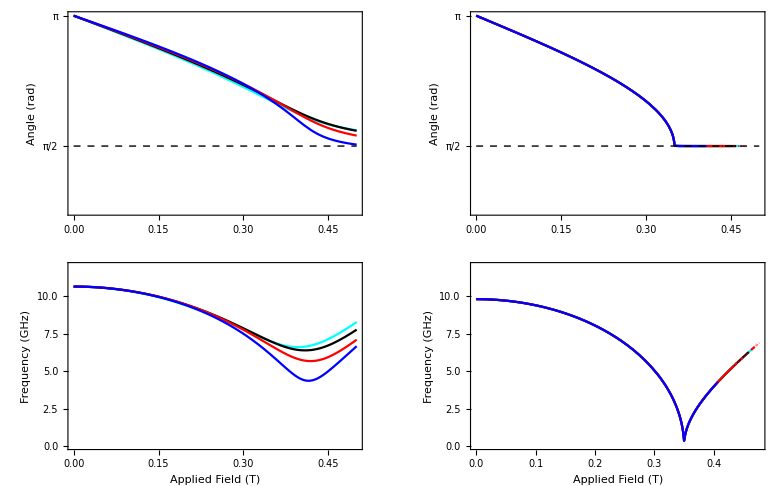

```mathematica
f[H_,Heff_,Hstr_,ang_,a_]:= 28 Sqrt[(H Sin[ang]+ Hstr Cos[ang-a*H]+Heff Cos[2 ang])(H Sin[ang]+Hstr Cos[ang-a*H]+Heff Cos[ang]^2)]
GraphicsGrid[{{Plot[{θ[H,0.35,-0.03,0],θ[H,0.35,-0.03,1],θ[H,0.35,-0.03,2],θ[H,0.35,-0.03,3],Pi/2},{H,0,0.5},PlotRange->{Pi/4,Pi},Frame->True,FrameTicks->{{{0,Pi/2,Pi},None},Automatic},FrameLabel->{" ","Angle (rad)"},ImageSize->Medium,PlotStyle->{Cyan,Black, Red,Blue,{Black,Thin,Dashed}}],
Plot[{θ[H,0.35,-0.00001,0]//Chop,θ[H,0.35,-0.00001,1]//Chop,θ[H,0.35,-0.00001,2]//Chop,θ[H,0.35,-0.00001,3]//Chop,Pi/2},{H,0,0.5},PlotRange->{Pi/4,Pi},Frame->True,FrameTicks->{{{0,Pi/2,Pi},None},Automatic},FrameLabel->{" ","Angle (rad)"},ImageSize->Medium,PlotStyle->{Cyan,Black,Red,Blue, {Black,Thin,Dashed}}]
},{
Plot[{f[H,0.35,-0.03,θ[H,0.35,-0.03,0]//Chop,0],f[H,0.35,-0.03,θ[H,0.35,-0.03,1]//Chop,1],f[H,0.35,-0.03,θ[H,0.35,-0.03,2]//Chop,2],f[H,0.35,-0.03,θ[H,0.35,-0.03,3]//Chop,3]},{H,0,0.5},Frame->True,FrameLabel->{"Applied Field (T)","Frequency (GHz)"},PlotStyle->{Cyan,Black,Red,Blue},PlotRange-> {0,12},ImageSize->Medium],
Plot[{f[H,0.35,-0.00001,θ[H,0.35,-0.00001,0]//Chop,0],f[H,0.35,-0.00001,θ[H,0.35,-0.00001,1]//Chop,1],f[H,0.35,-0.00001,θ[H,0.35,-0.00001,2]//Chop,2],f[H,0.35,-0.00001,θ[H,0.35,-0.00001,3]//Chop,3]},{H,0,0.5},Frame->True,FrameLabel->{"Applied Field (T)","Frequency (GHz)"},PlotStyle->{Cyan,Black,Red,Blue},PlotRange-> {0,12},ImageSize->Medium]}}]
```

```mathematica
Export[NotebookDirectory[]<>"freqvsField_with_Hstr_depend_on_field_alpha4.gif",%]
```

C:\Users\Jason\Desktop\jinting\STT_FMR\freqvsField_with_Hstr_depend_on_field_alpha4.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["C:\\Users\\Jason\\Desktop\\jinting\\STT_FMR\\freqvsField_with_Hstr_depend_on_field_alpha4.gif"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["C:\\Users\\Jason\\Desktop\\jinting\\STT_FMR\\freqvsField_with_Hstr_depend_on_field_alpha4.gif"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["C:\\Users\\Jason\\Desktop\\jinting\\STT_FMR\\freqvsField_with_Hstr_depend_on_field.gif"]]]
```

```mathematica
(*jinting_data*)


(* 60 nm diameter *)
C01L22F01J ={Range[0.14,0.50,0.02],{8.7998680,6.1034634,5.7551570,6.0999988,5.9914373,5.8596698,9.5428231,5.0988432,6.3997315,5.7999987,5.9999982,5.795802,7.6578162,5.1166327,9.7003246,5.336266,5.9815635,5.3794728,5.7758765}}//Transpose;
C01L22F02J ={Range[0.14,0.50,0.02],{14.5899832,12.5977833,11.9745068,10.2744868,10.0484807,10.9467829,13.4985602,9.3463487,8.8741817,8.5394599,8.1855284,7.8750809,5.1686546,7.4769565,6.607953,7.4142572,7.9240191,8.3832975,8.1154828}}//Transpose;

C01L23F01J ={Range[0.1,0.44,0.02],{7.9482842,8.1183145,12.0183427,11.8400301,11.9299499,11.8834538,11.7830337,11.5831115,11.3926908,11.1131226,10.8679971,10.566475,10.1166463,9.665535,9.2328347,8.7097568,8.6463691,7.8800621}}//Transpose;C01L23F02J ={Range[0.1,0.44,0.02],{12.9673979,12.0841386,11.3437774,14.3987007,13.8359585,14.1292696,14.5585063,14.7268152,13.997407,13.4975296,12.9975826,13.0999587,12.1974165,12.1959569,11.6991201,11.4989821,7.9892374 ,10.7001079}}//Transpose;

C01L25F01J ={Range[0.2,0.5,0.03],{6.4694377,7.0047229,5.5255541,5.7273129,7.2654832,7.101862,7.0726342,7.1632537,7.3116411,7.5615222,7.7724026}}//Transpose;
C01L25F02J={Range[0.2,0.5,0.03],{10.8639892,10.3258787,10.078844,9.7263611,9.3976065,14.9073334,8.6323722,8.2590657,8.163555,8.2615834,8.7673628}}//Transpose;
(* 70 nm diameter *)
C02L10F01J ={Range[0.15,0.45,0.03],{7.3179227,8.3475368,8.5150289,9.373798,9.4104097,9.2325043,8.8795455,8.1190621,7.3325058 ,6.9724032,7.2673535}}//Transpose;
C02L10F02J ={Range[0.15,0.45,0.03],{11.7521203,12.715393,12.5388081,11.0334494,13.8752913,11.4000081,11.2066497,10.6066438,9.6185859,7.7999729,3.0684253}}//Transpose;
C02L22F01J ={Range[0.16,0.46,0.02],{10.924382,10.9274553,10.7265949,10.3963367,10.131452,9.9243656,9.6234218,9.2490614,8.8286331,8.4650789,8.0397284,7.715779,7.1434355,6.8093074,6.6643274,6.767728
}}//Transpose;
C02L22F02J ={Range[0.16,0.46,0.02],{12.6953112,12.3817408,12.3040604,12.1824277,12.0671809,11.7889712,11.9958577,11.3941412,2.0014536,2.001393,10.3999547,10.0999954,2.001579,8.8999392,8.8997082,8.7994921}}//Transpose;
C02L23F01J ={Range[0.16,0.44,0.02],{11.2002911,11.2955171,11.3314534,11.1562386,10.9022539,10.577916,10.1391425,9.8000471,9.376425,9.1283773,8.2575269,7.886649,8.3151482,7.7506476,7.1175634}}//Transpose;
C02L23F02J ={Range[0.16,0.44,0.02],{8.4000141,12.9694413,12.8883867,12.8237932,12.5263673,12.2474508,11.9291782,11.6177779,12.2946388,11.5067835,4.8514158,10.3971251,9.9158956,9.6094137,9.2101291
}}//Transpose;

(* 100 nm diameter *)
C00L24F01J ={{0.14,0.17,0.2,0.23,0.26,0.29,0.32,0.35,0.38,0.41,0.44,0.47,0.5},{6.8999989,6.9025019,2.0063448,2.0000001,9.3476225,5.0986757,6.9191068,13.5301329,2.9990585,2.3306839,5.0116845,5.8962632,4.2919443}}//Transpose;

C00L24F02J ={{0.14,0.17,0.2,0.23,0.26,0.29,0.32,0.35,0.38,0.41,0.44,0.47,0.5},{11.4102083,11.0741513,10.6576297,9.9957236,8.1085865,8.1321014,13.7999659,5.6715086,5.0145136,5.4991683,6.2571734,6.7778793,7.1469453}}//Transpose;
```

```mathematica
C00L22F01J ={Range[0.15,0.45,0.03],{10.4225418,13.9999592,5.4999998,5.2924179,7.3060335,3.9888595,2.978049,3.8347323,4.0408831,4.3917914,6.1375893}}//Transpose;

C00L22F02J ={Range[0.15,0.45,0.03],{11.8999298,10.0122608,9.4201296,8.0841384,.7187783,9.1633012,4.9068669,5.0459833,5.2486122,5.3881796,6.5000008}}//Transpose;
```

```mathematica
C00L23F01J ={Range[0.1,0.44,0.02],{7.8232859,5.7991699,6.2999816,7.4995161,7.1012281,6.2000393,5.9002353,5.8999226,5.2006404,3.6903967,3.8478016,5.1098223,7.6513764,6.0366183,6.6902609,11.3012866,7.78933,6.1026139}}//Transpose;

C00L23F02J ={Range[0.1,0.44,0.02],{10.925376,10.4976672,10.3267061,10.5966786,10.4492997,10.1996557,9.954376,9.6032918,9.0143059,8.8373082,8.5546954,10.3843536,10.8114665,9.559046,9.0800754,8.7434649,10.4,10.1932328}}//Transpose;
```

```mathematica
(* 80 nm diameter *)
```

```mathematica
C03L10F01J ={Range[0.18,0.45,0.03],{9.4529355,9.1906254,10.4245889,8.2013736,7.6212899,7.2772759,6.9350335,6.676052,6.8200441,7.1094128
}}//Transpose;
C03L10F02J ={Range[0.18,0.45,0.03],{10.8025181,11.1,7.2302834,11.0390272,10.3346374,9.8558994,9.2396577,8.5129646,8.123401,8.0472654
}}//Transpose;
C03L22F01J ={Range[0.14,0.44,0.02],{8.2156605,7.7963755,7.6097399,7.0655081,6.9857853,6.7313778,6.7959909,6.5834557,6.2041486,4.2210742,2.9050927,3.2999922,3.438554,4.8605,5.2403034,5.677135}}//Transpose;
C03L22F02J ={Range[0.14,0.44,0.02],{11.0753583,10.9099559,10.820742,10.4179922,10.2043859,9.702054,9.4636155,9.0353298,8.3763716,8.2996439,4.128561,4.2868773,5.2735593,6.0386882,7.6999498,7.0321539}}//Transpose;
C03L23F01J ={Range[0.16,0.44,0.02],{6.5995593,6.9011561,5.4215474,5.2136557,6.412963,5.7001367,7.0608919,8.9067403,9.3426479,6.3719563,6.0230143,6.1154057,6.1339372,6.1571723,6.2578123}}//Transpose;
C03L23F02J ={Range[0.16,0.44,0.02],{10.5364471,10.5668343,10.7264802,10.8096459,8.2316305,9.6763265,8.4021117,10.099992,9.7989628,8.6075732,7.9935186,7.6208717,7.468523,7.5116767,7.3626159}}//Transpose;
```

```mathematica
(* 50 nm diameter *)
```

```mathematica
C00L16F01J ={Range[0.2,0.5,0.02],{11.1079721,10.7520868,10.4412044,10.2315673,9.9377569,9.5506446,4.222636,8.7618731,7.9384767,7.3013715,6.7605159,6.5390432,6.2263565,5.9325395,5.8984466,5.901534}}//Transpose;
C00L16F02J ={Range[0.2,0.5,0.02],{6.0999749,6.7999995,7.7993444,6.0012312,3.6281587,5.20008,9.114271,3.3869611,3.1452461,2.010467,4.1001516,3.9006849,3.9022973,2.3099861,3.6119982,3.8994912}}//Transpose;
C00L17F01J ={Range[0.16,0.5,0.02],{9.2627822,11.7999714,11.8251433,11.0375311,11.2435172,10.4373233,9.9204699,9.9100528,8.8460343,7.3643331,7.5361018,7.295827,6.4643115,5.6053234,4.9245128,4.9032071,4.8363816,5.19629}}//Transpose;
C00L17F02J ={Range[0.16,0.5,0.02],{12.2164204,8.3908781,8.2678567,7.7072211,7.8485903,13.8328779,13.5612687,13.8104801,13.2564469,11.8301043,11.9257966,12.0420596,11.1179696,6.0741928,5.7457022,5.6727133,6.813496,6.408542}}//Transpose;
```

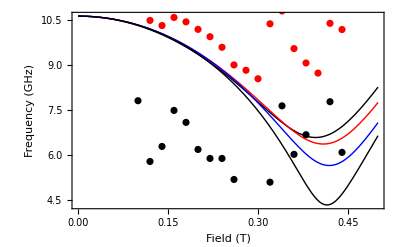

```mathematica
Show[Plot[{f[H,0.35,-0.03,θ[H,0.35,-0.03,0]//Chop,0],f[H,0.35,-0.03,θ[H,0.35,-0.03,1]//Chop,1],f[H,0.35,-0.03,θ[H,0.35,-0.03,2]//Chop,2],f[H,0.35,-0.03,θ[H,0.35,-0.03,3]//Chop,3]},{H,0,0.5},Frame->True,FrameLabel->{"Field (T)","Frequency (GHz)"},PlotStyle->{{Black,Thin},{Red,Thin},{Blue,Thin}}],ListPlot[{C00L23F01J,C00L23F02J},PlotStyle->{Black,Red,Blue}]]
```

```mathematica
Manipulate[Show[Plot[f[H,Keff,Hstr,θ[H,Keff,Hstr,a]//Chop,a],{H,0,0.55},PlotRange->{0,15}],ListPlot[{C00L23F01J,C00L23F02J},PlotRange->{0,13}]],{Keff,0.2,0.6},{a,0.1,3},{Hstr,-0.4,-0.00001}]
```